# Single infection with trophical transmission

## Ecological dynamics of a resident

```mathematica
dIsdt = R[Iw, Is]- d Is- Π0[Ds, Dw] Is  - γw W Is ;(*Susceptible intermediate*)
dIwdt =  γw W Is  - (d + α)Iw - Π1[Ds, Dw, βw]Iw; (*Infected intermediate*)
dDsdt =B[Ds, Dw, Is, Iw]  - μ Ds - λ[βw, Iw] Ds;  (*Susceptible definitive*)
dDwdt =λ[βw, Iw] Ds- (μ + σ) Dw ;(*Infected definitive*)
dWdt = fw Dw - δ W - γw W Is;
```

```mathematica
func0 = {R[Iw, Is] -> r(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
func1 =  {R[Iw, Is] -> r(1- (Is + Iw)/Κ)(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
var = {Is, Iw, Ds, Dw, W};
vart = {Is[t], Iw[t], Ds[t], Dw[t], W[t]};
sys = {dIsdt, dIwdt, dDsdt, dDwdt, dWdt};
```

```mathematica
solW0 = Solve[Thread[sys == 0]/.func0/.W-> 0,{Is, Iw, Ds, Dw}]
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-d+r)/ρ,Dw→0}}

```mathematica
solW0Func1= Solve[Thread[sys == 0]/.func1/.W-> 0,{Is, Iw, Ds, Dw}]//FullSimplify
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→Κ-(d Κ)/r,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-r μ+c (-d+r) Κ ρ)/(c Κ ρ^2),Dw→0}}

Stability of the equilibrium

## Linear functions

```mathematica
A = {{r - d - Π0[Ds, Dw] - γw W, r, 0, 0, 0}, {γw W, - (d + α)-  Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
A//MatrixForm
```

(-d+r-W γw-Π0[Ds,Dw] | r | 0 | 0 | 0
W γw | -d-α-Π1[Ds,Dw,βw] | 0 | 0 | 0
0 | 0 | -Iw βw-μ+c (Is+Iw) ρ | c (Is+Iw) ρ | 0
0 | 0 | Iw βw | -μ-σ | 0
0 | 0 | 0 | fw | -Is γw-δ)

```mathematica
(A.var /.func0)== (sys/.func0)//FullSimplify
```

True

```mathematica
Aeigens = Eigenvalues[A/.func0];
```

```mathematica
FullSimplify[Aeigens/.solW0[[1]]/.W-> 0, Assumptions->{α>0, r>0, σ>0}]
```

{-δ,-d-α,-d+r,-μ-σ,-μ}

```mathematica
FullSimplify[Aeigens/.solW0[[2]]/.W-> 0, Assumptions->{r>0, d>0,μ>0, σ>0, ρ>0, α>0, βw>0}]
```

{-δ-(γw μ)/(c ρ),-(-d βw+r βw+(r+α) ρ+Abs[-d βw+r βw+(r+α) ρ])/(2 ρ),Piecewise[{{(d βw-α ρ-r (βw+ρ))/ρ, d βw>α ρ+r (βw+ρ)}, {0, True}}],-μ-σ,0}

## Logistic growth intermediate hosts

```mathematica
AFunc1 = {{r(1-(Is + Iw)/Κ) - d - Π0[Ds, Dw]-  γw W, r(1-(Is + Iw)/Κ), 0, 0, 0}, {γw W, - (d + α)- Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
(AFunc1/.func1).var == (sys/.func1)//FullSimplify
```

True

```mathematica
AeigensFunc1 = Eigenvalues[AFunc1/.func1]//FullSimplify
```

{-Is γw-δ,-1/(2 Κ)(Is r+Iw r+√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),-1/(2 Κ)(Is r+Iw r-√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ-√((Iw βw+c (Is+Iw) ρ)^2+2 (-Iw βw+c (Is+Iw) ρ) σ+σ^2)),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ+√((Iw βw+c (Is+Iw) ρ)^2+2 (-Iw βw+c (Is+Iw) ρ) σ+σ^2))}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[2]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d, (c p (-d+r) Κ+r σ)>0}]
```

{-δ+((d-r) γw Κ)/r,-d-α,0,-(c p (d-r) Κ+r (2 μ+σ)+Abs[c p (-d+r) Κ+r σ])/(2 r),(c p (-d+r) Κ-r (2 μ+σ)+Abs[c p (-d+r) Κ+r σ])/(2 r)}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[3]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d,  c> 0, μ+σ>0, p>0}]
```

{-δ-(γw μ)/(c p),-(c p (p (r+α)+(-d+r) βw) Κ-r (p+βw) μ+√((c p (p (r+α)+(-d+r) βw) Κ-r (p+βw) μ)^2))/(2 c p^2 Κ),(-c p (p (r+α)+(-d+r) βw) Κ+r (p+βw) μ+√((c p (p (r+α)+(-d+r) βw) Κ-r (p+βw) μ)^2))/(2 c p^2 Κ),-μ-σ,0}

```mathematica
makeSystem[var_, vart_, sys_]:= (syst = sys/.Thread[var-> vart]; sysfull = Thread[D[vart, t] == syst]);
```

Numerical analysis

```mathematica
sysFunc0 = makeSystem[var,vart ,  sys/.func0];
sysFunc1 = makeSystem[var,vart ,  sys/.func1];
```

```mathematica
prEco = {r -> 1.5, d -> 1.7, ρ -> 1.2,γw -> 4.5, α-> 0, βw-> 2.5, c-> 0.4, μ-> 1.9, σ-> 0, fw -> 14.5, δ-> 1.9};
```

```mathematica
maxt = 100;
initFunc0= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 30 };
NSolve[Thread[(sys/.func0/.prEco) == 0], var];
ndsol0Func0 = NDSolve[Join[sysFunc0/.prEco, initFunc0], var, {t, 0, maxt}]
```

{{Is→InterpolatingFunction[{{0., 100.}}, <>],Iw→InterpolatingFunction[{{0., 100.}}, <>],Ds→InterpolatingFunction[{{0., 100.}}, <>],Dw→InterpolatingFunction[{{0., 100.}}, <>],W→InterpolatingFunction[{{0., 100.}}, <>]}}

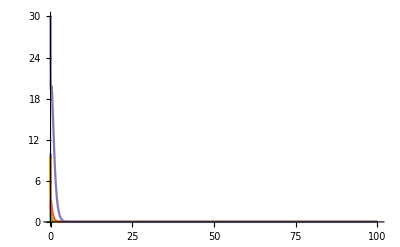

```mathematica
Plot[Evaluate[vart/.ndsol0Func0], {t, 0, maxt}, PlotRange->All]
```

```mathematica
prEcoFunc1 = {r -> 4.5, d -> 1.1, ρ-> 1.2,γw -> 5.5, α-> 0, βw-> 1.5, c-> 0.4, μ-> 0.9, σ-> 0, fw -> 14.5, δ-> 1.9, Κ-> 200};
maxt = 100;
initFunc1= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 10 };
NSolve[Thread[(sys/.func1/.prEcoFunc1) == 0], var]
ndsol0Func1 = NDSolve[Join[sysFunc1/.prEcoFunc1, initFunc1], var, {t, 0, maxt}]
```

{{Is→151.111,Iw→0.,Ds→0.,Dw→0.,W→0.},{Is→151.711,Iw→-0.6,Ds→0.0456209,Dw→-0.0456209,W→-0.000790977},{Is→-0.345455,Iw→151.457,Ds→0.,Dw→0.,W→-87.6854},{Is→0.35874,Iw→1.51626,Ds→0.39453,Dw→0.997016,W→3.73263},{Is→17.3293,Iw→-15.4543,Ds→0.0121495,Dw→-0.312937,W→-0.0466777},{Is→-1.88109,Iw→3.75609,Ds→0.109991,Dw→0.688562,W→-1.18212},{Is→1.875,Iw→0.,Ds→2.79818,Dw→0.,W→0.},{Is→0.6,Iw→-0.6,Ds→0.0717241,Dw→-0.0717241,W→-0.2},{Is→-0.345455,Iw→0.345455,Ds→0.,Dw→0.,W→-0.2},{Is→0.,Iw→0.,Ds→0.,Dw→0.,W→0.}}

{{Is→InterpolatingFunction[{{0., 100.}}, <>],Iw→InterpolatingFunction[{{0., 100.}}, <>],Ds→InterpolatingFunction[{{0., 100.}}, <>],Dw→InterpolatingFunction[{{0., 100.}}, <>],W→InterpolatingFunction[{{0., 100.}}, <>]}}

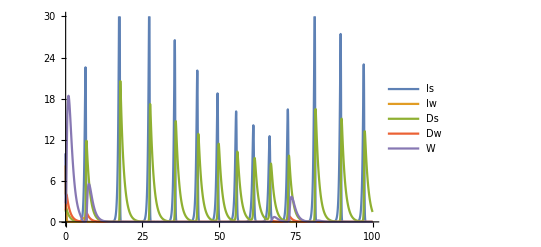

```mathematica
Plot[Evaluate[vart/.ndsol0Func1], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 30}}, PlotLegends->{"Is", "Iw", "Ds","Dw", "W"}]
```

## Mutant dynamics

```mathematica
dImudt = γm M Is  - (d + α)Imu -(Ds+Dw) (ρ+βm)Imu; (*Infected intermediate*)
dDmdt = Imu βm Ds - (μ + σ)Dm;
dMdt = fm Dm - δ M - γm Is M;
```

```mathematica
Am = {{-d-α - (Ds+Dw) (ρ+βm), 0, γm Is},{βm Ds, -μ -σ, 0},{0, fm, -δ- γm Is}};
Am//MatrixForm
```

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
Am.{Imu, Dm, M} == {dImudt, dDmdt, dMdt}//FullSimplify
```

True

```mathematica
FMat = {{0, 0, 0},{0, 0, 0}, {0, fm, 0}};
```

```mathematica
VMat ={{d+α+(Ds+Dw) (ρ+βm), 0, - Is γm},{-Ds βm, μ + σ, 0}, {0, 0, Is γm + δ}};
```

```mathematica
FMat - VMat == Am//FullSimplify
FMat-VMat//MatrixForm
```

True

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
R0 = Eigenvalues[FMat.Inverse[VMat]][[3]]//FullSimplify
```

(Ds fm Is βm γm)/((Is γm+δ) (d+α+(Ds+Dw) (βm+ρ)) (μ+σ))

R0=fm/(Is γm+δ)(Is  γm)/(d+α+(Ds+Dw) (ρ+βm))(Ds  βm)/(μ+σ)

```mathematica
R0res = R0/.Dw-> 0/.Is->μ/(c p)/.Ds->(-d+r)/p/.fm -> fw/.γm-> γw/.βm-> βw//FullSimplify
```

(fw (-d+r) βw γw μ)/((p (r+α)+(-d+r) βw) (c p δ+γw μ) (μ+σ))

```mathematica
Reduce[R0res>1 && fw > 0 && r>0 && d >0 && βw >0 && γw > 0 && μ > 0 && p > 0 && c > 0 && α>0 && μ > 0 && σ > 0&& δ > 0]//FullSimplify
```

σ>0&&μ>0&&α>0&&r>0&&fw>-((p (r+α)+(-d+r) βw) (μ+σ))/((d-r) βw)&&βw>0&&γw>0&&δ>0&&0<c<(γw μ (-1+(fw (-d+r) βw)/((p (r+α)+(-d+r) βw) (μ+σ))))/(p δ)&&((p>0&&0<d<r)||(d>r&&0<p<((d-r) βw)/(r+α)))

```mathematica
-((p (r+α)+(-d+r) βw) (μ+σ))/((d-r) βw)/.prEco
```

-12.74

```mathematica
fw/.prEco
```

14.5

```mathematica
(γw μ (-1+(fw (-d+r) βw)/((p (r+α)+(-d+r) βw) (μ+σ))))/(p δ)/.prEco
```

-20.6781

```mathematica
prEco
```

{r→1.5,d→1.1,p→1.2,γw→4.5,α→0,βw→2.5,c→0.4,μ→4.9,σ→0,fw→14.5,δ→1.9}

```mathematica
((d-r) βw)/(r+α)/.prEco
```

-0.666667